```mathematica
mm[j_,m_]:=1-m(Floor[j/m]-Floor[(j-1)/m])
mm2[j_,m_]:=1/j-(Floor[j/m]-Floor[(j-1)/m])/Floor[j/m]
mm3[j_,m_]:=1/j-If[j<m,0,(1+Ceiling[(1-j)/m]/Floor[j/m])]
mm4[j_,m_]:=1/j-If[j<m,0,(1-Floor[(-1+j)/m]/Floor[j/m])]
```

```mathematica
Table[mm[n,4],{n,1,10}]
```

{1,1,1,-3,1,1,1,-3,1,1}

```mathematica
N@Sum[mm[j,5/2]/j,{j,1,1000}]
```

1.12674

```mathematica
Log[2.5]
```

0.916291

```mathematica
HarmonicNumber[x]-HarmonicNumber[x/2.5]/.x->1000.
```

0.915541

```mathematica
Table[1/j,{j,1,20}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20}

```mathematica
Table[1/j-(HarmonicNumber[Floor[j/2.5]]-HarmonicNumber[Floor[(j-1)/2.5]]),{j,1,20}]
```

{1,1/2,-2/3,1/4,-3/10,1/6,1/7,-5/24,1/9,-3/20,1/11,1/12,-8/65,1/14,-1/10,1/16,1/17,-11/126,1/19,-3/40}

```mathematica
Table[(HarmonicNumber[Floor[j/2.5]]-HarmonicNumber[Floor[(j-1)/2.5]]),{j,1,20}]
```

{0,0,1,0,1/2,0,0,1/3,0,1/4,0,0,1/5,0,1/6,0,0,1/7,0,1/8}

```mathematica
N@Sum[mm4[n,E],{n,1,100000}]
```

1.00002

```mathematica
FullSimplify[(Floor[j/m]-Floor[(j-1)/m])/Floor[j/m]]
```

1+Ceiling[(1-j)/m]/Floor[j/m]

```mathematica
Log[5./2.]
```

0.916291

```mathematica
1-Floor[(j-1)/m]/Floor[j/m]
```

1-Floor[(-1+j)/m]/Floor[j/m]

```mathematica
Table[1-Floor[(j-1)/E]/Floor[j/E],{j,3,20}]
```

{1,0,0,1/2,0,0,1/3,0,1/4,0,0,1/5,0,0,1/6,0,0,1/7}

```mathematica
Expand[Floor[(-1+j)/m]/Floor[j/m]]
```

Floor[(-1+j)/m]/Floor[j/m]

```mathematica
Table[(Floor[j/E]-Floor[(j-1)/E])/Floor[j/E],{j,3,20}]
```

{1,0,0,1/2,0,0,1/3,0,1/4,0,0,1/5,0,0,1/6,0,0,1/7}

```mathematica
Clear[lg]
mm4[j_,m_]:=1/j-If[j<m,0,(1-Floor[(-1+j)/m]/Floor[j/m])]
lg[n_,0,m_]:=UnitStep[n]
lg[n_,k_,m_]:=lg[n,k,m]=Sum[mm4[j,m]lg[n-j,k-1,m],{j,1,n}]
lz[n_,z_,m_]:=Sum[z^k/k! lg[n,k,m],{k,0,n}]
dlz[n_,z_,m_]:=lz[n,z,m]-lz[n-1,z,m]
```

```mathematica
Table[dlz[n,1,E],{n,1,40}]
```

{1,1,0,0,0,0,0,0,0,0,-1/4,0,0,1/20,0,0,1/30,0,0,1/42,0,-3/32,-3/224,0,47/1440,-7/1440,0,41/1800,-1/1800,-1/11,761/46200,79/46200,51/1408,-3061/221760,137/443520,1819/74880,-1297/262080,-59/524160,22033/1310400,-99/509600}

```mathematica
dif[x_,b_,s_]:=HarmonicNumber[x,s]-HarmonicNumber[x/b,s]
```

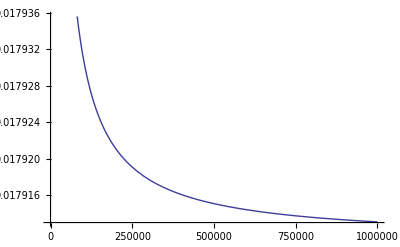

```mathematica
Plot[Abs[dif[n,10,1+100I]],{n,1,1000000}]
```

```mathematica
FullSimplify[Sum[t^j/ j^s,{j,1,x}]]
```

-t^(1+x) LerchPhi[t,s,1+x]+PolyLog[s,t]